```mathematica
Needs["DatabaseLink`"];
DatabaseExplorer[]
```

7gerq_shm20FrontEndObject[LinkObject["7gerq_shm", 3, 1]]20Database Explorer

```mathematica
Needs["DatabaseLink`"];
conn=OpenSQLConnection["publisher"];
```

```mathematica
SQLExecute[conn,"SELECT * FROM ROYSCHED WHERE ROYALTY >= .11 AND ROYALTY <= .12"]//TableForm
```

BS1011 | 5001 | 50000 | 0.12
CP5018 | 2001 | 4000 | 0.12
BS1001 | 1001 | 5000 | 0.12
PY2002 | 1001 | 5000 | 0.12
PY2003 | 2001 | 5000 | 0.12
UK3004 | 1001 | 2000 | 0.12
CK4005 | 2001 | 6000 | 0.12
CP5010 | 5001 | 50000 | 0.12
PY2012 | 5001 | 50000 | 0.12
PY2013 | 5001 | 50000 | 0.12
UK3006 | 1001 | 2000 | 0.12
BS1014 | 4001 | 8000 | 0.12
UK3015 | 2001 | 4000 | 0.12
CK4016 | 5001 | 15000 | 0.12
CK4017 | 2001 | 8000 | 0.12
BS1007 | 5001 | 50000 | 0.12

```mathematica
SQLExecute[conn,"SELECT T.TITLE, T.TITLE_ID, MIN(R.ROYALTY) ROYALTY FROM ROYSCHED R, TITLES T LEFT OUTER JOIN ROYSCHED ON T.TITLE_ID = R.TITLE_ID GROUP BY T.TITLE, T.TITLE_ID ORDER BY ROYALTY, T.TITLE DESC","ShowColumnHeadings"->True]//TableForm
```

TITLE | TITLE_ID | ROYALTY
Where Minds Meat: The Impact of Diet on Behavior | PY2013 | 0.1
Treasures of the Sierra Madre | UK3015 | 0.1
Too Many Cooks | CK4016 | 0.1
The Net: Feeding Trolls and Eating Spam | CP5009 | 0.1
Taiwan Trails | CP5010 | 0.1
Sticky Software: UI and GUI | CP5018 | 0.1
Self Hypnosis: A Beginner's Guide | PY2002 | 0.1
Phobic Psychology | PY2003 | 0.1
Modems for Morons | BS1007 | 0.1
Made to Wonder: Cooking the Macabre | CK4005 | 0.1
Let Them Eat Cake! | CK4017 | 0.1
Know Thyself | PY2012 | 0.1
How to Burn a Compact Disk | UK3006 | 0.1
How Green Is My Valley? | PY2008 | 0.1
Hamburger Again! | UK3004 | 0.1
Guide to Impractical Databases | BS1011 | 0.1
Exit Interviews | BS1014 | 0.1
Designer Class Action Suits | BS1001 | 0.1

```mathematica
CloseSQLConnection[conn];
```

```mathematica
conn=OpenSQLConnection["demo"]
```

SQLConnection[…]

```mathematica
conn1=OpenSQLConnection[];
```

```mathematica
%12
```

SQLConnection[…]

```mathematica
SQLTables[conn]
```

{SQLTable[SAMPLETABLE1,TableType→TABLE]}

```mathematica
SQLTables[conn1]
```

{SQLTable[SAMPLETABLE1,TableType→TABLE]}

```mathematica
SQLColumns[conn,"SAMPLETABLE1"]//TableForm
```

SQLColumn[{SAMPLETABLE1,ENTRY},DataTypeName→INTEGER,DataLength→32,Default→Null,Nullable→1]
SQLColumn[{SAMPLETABLE1,VALUE},DataTypeName→DOUBLE,DataLength→64,Default→Null,Nullable→1]
SQLColumn[{SAMPLETABLE1,NAME},DataTypeName→VARCHAR,DataLength→16,Default→Null,Nullable→1]

```mathematica
data=SQLSelect[conn,"SAMPLETABLE1"]
```

{{1,5.6,Day1},{2,5.9,Day2},{3,7.2,Day3},{4,6.2,Day4},{5,6.,Day5}}

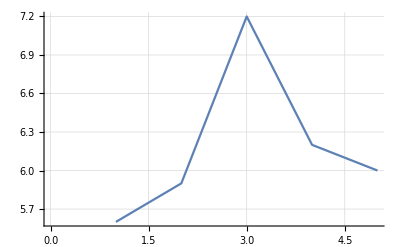

```mathematica
ListLinePlot[data[[All,2]],GridLines->Automatic]
```

```mathematica
SQLSelect[conn,"SAMPLETABLE1","ShowColumnHeadings"->True]//TableForm
```

ENTRY | VALUE | NAME
1 | 5.6 | Day1
2 | 5.9 | Day2
3 | 7.2 | Day3
4 | 6.2 | Day4
5 | 6. | Day5

```mathematica
SQLInsert[conn,"SAMPLETABLE1",{"ENTRY","VALUE","NAME"},{6,8.2,"Day5"}]
```

1

```mathematica
SQLInsert[conn,"SAMPLETABLE1",{"ENTRY","VALUE","NAME"},{7,9.2,"Day6"}]
```

1

```mathematica
SQLInsert[conn,"SAMPLETABLE1",{"ENTRY","VALUE","NAME"},{8,10.2,"Day7"}]
```

1

```mathematica
SQLSelect[conn,"SAMPLETABLE1","ShowColumnHeadings"->True]//TableForm
```

ENTRY | VALUE | NAME
1 | 5.6 | Day1
2 | 5.9 | Day2
3 | 7.2 | Day3
4 | 6.2 | Day4
5 | 6. | Day5
6 | 8.2 | Day6
6 | 8.2 | Day5
7 | 9.2 | Day6
8 | 10.2 | Day7

```mathematica
SQLUpdate[conn,"SAMPLETABLE1",{"VALUE"},{7},SQLColumn["VALUE"]>8]
```

4

```mathematica
SQLSelect[conn,"SAMPLETABLE1","ShowColumnHeadings"->True]//TableForm
```

ENTRY | VALUE | NAME
1 | 5.6 | Day1
2 | 5.9 | Day2
3 | 7.2 | Day3
4 | 6.2 | Day4
5 | 6. | Day5
6 | 7. | Day6
6 | 7. | Day5
7 | 7. | Day6
8 | 7. | Day7

```mathematica
SQLUpdate[conn,"SAMPLETABLE1",{"VALUE"},{11},SQLColumn["ENTRY"]==6]
```

2

```mathematica
SQLSelect[conn,"SAMPLETABLE1","ShowColumnHeadings"->True]//TableForm
```

ENTRY | VALUE | NAME
1 | 5.6 | Day1
2 | 5.9 | Day2
3 | 7.2 | Day3
4 | 6.2 | Day4
5 | 6. | Day5
7 | 7. | Day6
8 | 7. | Day7
6 | 11. | Day6
6 | 11. | Day5

```mathematica
SQLUpdate[conn,"SAMPLETABLE1",{"VALUE"},{11},SQL
```